# Inlämningsuppgift 2

IX1307 Problemlösning i Matematik, Inlämningsuppgift 1a, HT2019
Nikita Heinonen, nikitah@kth.se

## Data

### Kol (TWh)

```mathematica
kol={{1990.,25845.88485},{1991.,25561.41954},{1992.,25478.81089},{1993.,25580.92144},{1994.,25729.64169},{1995.,25867.8533},{1996.,26516.28457},{1997.,26549.71899},{1998.,26351.79429},{1999.,26492.77461},{2000.,27403.94562},{2001.,27851.05371},{2002.,28936.6423},{2003.,31475.58334},{2004.,33656.31109},{2005.,36118.94545},{2006.,37979.81684},{2007.,40143.91171},{2008.,40712.5427},{2009.,40088.33994},{2010.,41932.74507},{2011.,43948.96889},{2012.,44129.62497},{2013.,44953.01385},{2014.,44916.83781},{2015.,43786.8458},{2016.,43101.23216},{2017.,43397.13549}};
```

### Olja (TWh)

```mathematica
olja={{1990.,37736.94729},{1991.,37763.14824},{1992.,38422.53103},{1993.,38179.42324},{1994.,39021.80173},{1995.,39555.43054},{1996.,40480.1731},{1997.,41544.67299},{1998.,41768.48384},{1999.,42510.09274},{2000.,43038.62001},{2001.,43421.10755},{2002.,43796.55068},{2003.,44803.21017},{2004.,46503.96733},{2005.,47115.72728},{2006.,47732.19992},{2007.,48471.73162},{2008.,48250.64229},{2009.,47422.36853},{2010.,48949.72046},{2011.,49455.27172},{2012.,50065.86499},{2013.,50698.38455},{2014.,51109.97172},{2015.,52053.27008},{2016.,53001.86598},{2017.,53752.27638}};
```

### Naturgas (TWh)

```mathematica
naturgas={{1990.,19486.64542},{1991.,19984.58677},{1992.,20076.92098},{1993.,20275.09431},{1994.,20405.36342},{1995.,21121.78818},{1996.,22143.41796},{1997.,22082.05319},{1998.,22485.93806},{1999.,23107.57158},{2000.,24019.89227},{2001.,24367.11133},{2002.,25108.12839},{2003.,25769.17552},{2004.,26752.16794},{2005.,27537.09099},{2006.,28347.57835},{2007.,29580.25097},{2008.,30321.37836},{2009.,29477.9263},{2010.,31759.12422},{2011.,32410.44868},{2012.,33270.53388},{2013.,33714.94785},{2014.,33986.84723},{2015.,34741.88349},{2016.,35741.82987},{2017.,36703.96587}};
```

### Kärnkraft (TWh)

```mathematica
karnkraft={{1990.,2000.642591},{1991.,2096.356868},{1992.,2112.277946},{1993.,2185.016841},{1994.,2226.050783},{1995.,2322.592422},{1996.,2407.002623},{1997.,2390.480054},{1998.,2431.571247},{1999.,2524.546817},{2000.,2580.976669},{2001.,2653.821898},{2002.,2696.204132},{2003.,2641.599256},{2004.,2757.124087},{2005.,2769.046942},{2006.,2803.605088},{2007.,2746.479825},{2008.,2737.860822},{2009.,2699.245242},{2010.,2767.507814},{2011.,2651.771616},{2012.,2472.44864},{2013.,2491.705601},{2014.,2541.027341},{2015.,2575.664304},{2016.,2612.83283},{2017.,2635.561104}};
```

### Bio-bränslen (TWh)

```mathematica
biobransle={{1990.,11111.11111},{1991.,11242.7549},{1992.,11375.95839},{1993.,11510.74008},{1994.,11647.11865},{1995.,11785.11302},{1996.,11924.74234},{1997.,12066.02598},{1998.,12208.98355},{1999.,12414.05573},{2000.,12500.},{2001.,12500.},{2002.,12470.},{2003.,12328.70237},{2004.,12159.75217},{2005.,12076.14729},{2006.,11993.11724},{2007.,11910.65806},{2008.,11828.76583},{2009.,11747.43666},{2010.,11666.66667},{2011.,11553.3766},{2012.,11441.18663},{2013.,11330.0861},{2014.,11220.06442},{2015.,11111.11111},{2016.,11003.2158},{2017.,10895.32049}};
```

### Andra förnybara energikällor (TWh)

```mathematica
andrafornybara={{1990.,116.4628246},{1991.,121.4122701},{1992.,130.3448548},{1993.,134.7069628},{1994.,139.8004029},{1995.,145.5958811},{1996.,149.6884804},{1997.,160.9528063},{1998.,168.4548712},{1999.,177.1371664},{2000.,185.2722028},{2001.,191.0179267},{2002.,205.6996386},{2003.,217.2027959},{2004.,234.3682046},{2005.,254.3922875},{2006.,271.7633551},{2007.,294.2977297},{2008.,314.3656167},{2009.,338.2157334},{2010.,378.0383427},{2011.,397.4546676},{2012.,430.3624386},{2013.,463.9825019},{2014.,504.3899227},{2015.,538.2067786},{2016.,556.9861292},{2017.,586.1710901}};
```

### Vattenkraft (TWh)

```mathematica
vatten={{1990.,2161.045291},{1991.,2213.110915},{1992.,2211.503167},{1993.,2344.266136},{1994.,2359.685227},{1995.,2488.983207},{1996.,2523.481143},{1997.,2569.633113},{1998.,2590.551798},{1999.,2608.338262},{2000.,2654.953445},{2001.,2586.668594},{2002.,2633.835653},{2003.,2629.430399},{2004.,2808.226932},{2005.,2918.064831},{2006.,3030.307944},{2007.,3079.79887},{2008.,3263.589026},{2009.,3253.601171},{2010.,3435.905581},{2011.,3503.227091},{2012.,3671.297583},{2013.,3797.954118},{2014.,3887.930335},{2015.,3891.408797},{2016.,4036.073668},{2017.,4059.868393}};
```

### Vindkraft (TWh)

```mathematica
vind={{1990.,3.632470516},{1991.,4.086706675},{1992.,4.733212019},{1993.,5.697568819},{1994.,7.122929844},{1995.,8.261923444},{1996.,9.204610762},{1997.,12.01757667},{1998.,15.91490057},{1999.,21.21534431},{2000.,31.41996387},{2001.,38.39098735},{2002.,52.33180737},{2003.,62.91691456},{2004.,85.11605376},{2005.,104.0868359},{2006.,132.8592792},{2007.,170.6860872},{2008.,220.5696719},{2009.,275.9292658},{2010.,341.5652412},{2011.,436.8034429},{2012.,523.8148612},{2013.,645.7219776},{2014.,712.4070431},{2015.,831.8262454},{2016.,959.4687163},{2017.,1122.74585}};
```

### Solenergi (TWh)

```mathematica
sol={{1990.,0.},{1991.,0.505223075},{1992.,0.468615413},{1993.,0.556737928},{1994.,0.60006443},{1995.,0.640874386},{1996.,0.705278679},{1997.,0.756655499},{1998.,0.880289501},{1999.,0.965823997},{2000.,1.177935576},{2001.,1.463956125},{2002.,1.831247734},{2003.,2.3293707},{2004.,3.054656084},{2005.,4.249617769},{2006.,5.818328387},{2007.,7.864870878},{2008.,12.72162081},{2009.,21.09259048},{2010.,33.82948514},{2011.,65.21188479},{2012.,100.9252749},{2013.,139.0442186},{2014.,197.6716635},{2015.,260.0058008},{2016.,328.1826964},{2017.,442.6183606}};
```

### Världens totala energikonsumtion (TWh)

```mathematica
totalt={{1990.,98462.371847116},{1991.,98987.38143285},{1992.,99813.54908523199},{1993.,100216.423316547},{1994.,101537.18489717401},{1995.,103296.25934793001},{1996.,106154.70010584098},{1997.,107376.31135546902},{1998.,108022.57284627101},{1999.,109856.69807370701},{2000.,112416.258116246},{2001.,113610.635952175},{2002.,115901.223848704},{2003.,119930.15013616001},{2004.,124960.08846344402},{2005.,128897.75152416898},{2006.,132297.06634468702},{2007.,136405.679742778},{2008.,137662.43593741},{2009.,135324.15543267998},{2010.,141265.10288404},{2011.,144422.53459229},{2012.,146106.05926769998},{2013.,148234.8407671},{2014.,149077.14748530003},{2015.,149790.2224058},{2016.,151341.68784990002},{2017.,153595.6630277}};
```

## Uppgift 1

### Uppskatta världens energikonsumtion år 2050.

Jag använder LinearModelFit för att ta fram en modell för funktionen. Jag väljer att använda mig av en linjär funktion då det verkar bäst passa tillhandahållen data.

```mathematica
model=LinearModelFit[totalt,x,x]
```

FittedModel[-4.51374×10^6+2314.87 x]

```mathematica
model[x]
```

-4.51374×10^6+2314.87 x

Nedan är grafen för den uppskattade energikonsumtionen fram till år 2050. Enligt modellen blir också den uppskattade energikonsumtionen år 2050 231747 TWh. Detta får jag reda på att trycka in 2050 som x-värde i modellen.

```mathematica
model[2050]
```

231747.

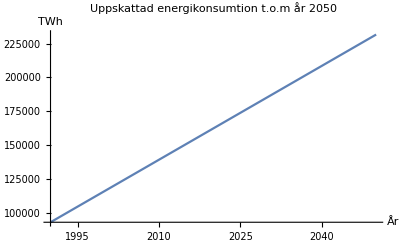

```mathematica
test=Plot[model[x],{x,1990,2050},AxesLabel->{"År","TWh"},PlotLabel->"Uppskattad energikonsumtion t.o.m år 2050"]
```

Nedan är den tillhandahållna informationen om energikonsumtionen mellan år 1990-2017.

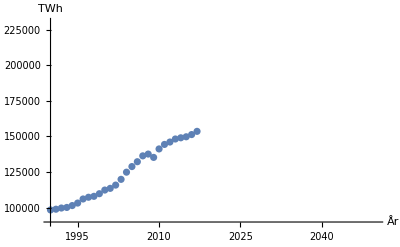

```mathematica
rawData=ListPlot[totalt,AxesLabel->{"År","TWh"},PlotRange->{{1990,2050},{90000,230000}}]
```

Nedan visas uppmätt data med uppskattad data enligt min modell.

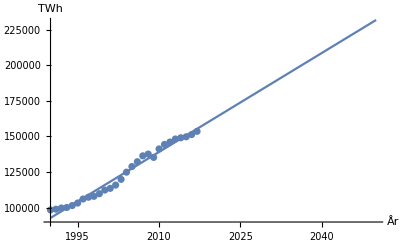

```mathematica
Show[rawData,test]
```

## Uppgift 2

### Uppskatta när olja som energikälla kan ersättas av förnybara energikällor.

Visa mätpunkterna för oljebaserad energi.

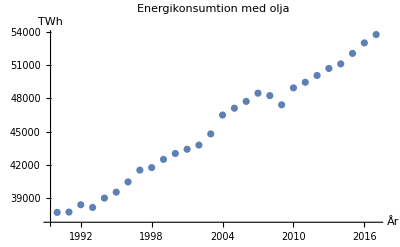

```mathematica
oil=ListPlot[olja,AxesLabel->{"År","TWh"},PlotLabel->"Energikonsumtion med olja"]
```

Adderar ihop alla förnybara energikällor. Sol, vind, Bio-bränslen, vatten och andra förnybara källor.
I uppgift tre kom jag på hur man kan automatiskt addera listor men kände inte att jag behövde göra om det här nedan då jag redan var färdig med uppgiften.

```mathematica
renew={{1990,11111.11111+116.4628246+2161.045291+3.632470516+0},{1991,0.505223075+4.086706675+2213.110915+121.4122701+11242.7549},{1992,11375.95839+130.3448548+2211.503167+4.733212019+0.468615413},{1993,0.556737928+5.697568819+2344.266136+134.7069628+11510.74008},{1994,11647.11865+139.8004029+2359.685227+7.122929844+0.60006443},{1995,0.640874386+8.261923444+2488.983207+145.5958811+11785.11302},{1996,11924.74234+149.6884804+2523.481143+9.204610762+0.705278679},{1997,0.756655499+12.01757667+2569.633113+149.6884804+11924.74234},{1998,12208.98355+168.4548712+2590.551798+15.91490057+0.880289501},{1999,0.965823997+21.21534431+2608.338262+177.1371664+12414.05573},{2000,12500+185.2722028+2654.953445+31.41996387+1.177935576},{2001,1.463956125+38.39098735+2586.668594+191.0179267+12500},{2002,12470+205.6996386+2633.835653+52.33180737+1.831247734},{2003,2.3293707+62.91691456+2629.430399+217.2027959+12328.70237},{2004,12159.75217+234.3682046+2808.226932+85.11605376+3.054656084},{2005,4.249617769+104.0868359+2918.064831+254.3922875+12076.14729},{2006,11993.11724+271.7633551+3030.307944+132.8592792+5.818328387},{2007,7.864870878+170.6860872+3079.79887+294.2977297+11910.65806},{2008,11828.76583+314.3656167+3263.589026+220.5696719+12.72162081},{2009,21.09259048+275.9292658+3253.601171+338.2157334+11747.43666},{2010,11666.66667+378.0383427+3435.905581+341.5652412+33.82948514},{2011,65.21188479+436.8034429+3503.227091+397.4546676+11553.3766},{2012,11441.18663+430.3624386+3671.297583+523.8148612+100.9252749},{2013,139.0442186+645.7219776+3797.954118+463.9825019+11330.0861},{2014,11220.06442+504.3899227+3887.930335+712.4070431+197.6716635},{2015,260.0058008+831.8262454+3891.408797+538.2067786+11111.11111},{2016,11003.2158+556.9861292+4036.073668+959.4687163+328.1826964},{2017,442.6183606+1122.74585+4059.868393+586.1710901+10895.32049}};
```

En graf som visar energikonsumtion med förnybara källor.

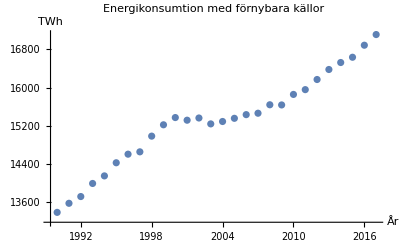

```mathematica
lp=ListPlot[renew,AxesLabel->{"År","TWh"},PlotLabel->"Energikonsumtion med förnybara källor"]
```

En rätlinjig anpassning till punkterna för oljebaserad energi.

```mathematica
lmoil=LinearModelFit[olja,x,x]
```

FittedModel[-1.16923×10^6+606.174 x]

Vi ser att den stämmer ok med datapunkterna.

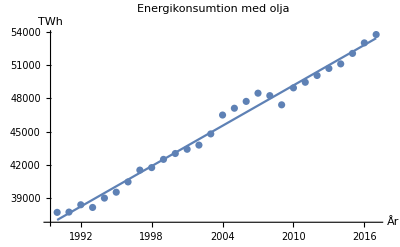

```mathematica
Show[oil,Plot[lmoil[x],{x,1990,2017}]]
```

En rätlinjig anpassning för förnybar energi.

```mathematica
lmrenew=LinearModelFit[renew,x,x]
```

FittedModel[-216412.+115.653 x]

Vi ser att den stämmer ok.

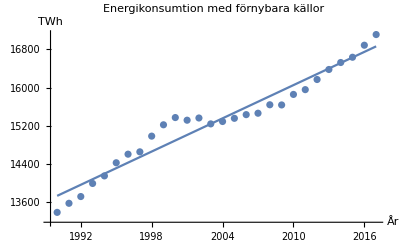

```mathematica
Show[lp,Plot[lmrenew[x],{x,1990,2017}]]
```

```mathematica
lmre=Plot[lmrenew[x],{x,1990,2017},PlotLabel->"Energikonsumtion",AxesLabel->{"År","TWh"}, PlotLabels->"Förnybara"];
```

```mathematica
lmoi=Plot[lmoil[x],{x,1990,2017},PlotLabels->"Olja"];
```

```mathematica
Show[lmre,lmoi,PlotRange->All]
```

-Graphics-

```mathematica
ekv1=Normal[lmoil]
```

-1.16923×10^6+606.174 x

```mathematica
ekv2=Normal[lmrenew]
```

-216412.+115.653 x

```mathematica
Solve[ekv1==ekv2,x]
```

{{x→1942.47}}

Vi ser redan att lutningen på oljegrafen är högre än för förnyelsebara. Detta betyder att med nuvarande modell kommer oljebaserad energi inte att tappa mot förnyelsebar och således inte kunna paseras. För matematikens skull försöker vi ändå lösa ekvationen ovan. Vi får svaret x=1942.47. Detta skulle representera år 1942 vilket är innan våra mätningar började. Detta beror på att oljans linje har mycket större lutning vilket gör att den korsar år-axeln längre ned. Detta bevisar att linjerna inte kommer mötas i framtiden.

## Uppgift 3

### Uppskatta om/när världens energikonsumtion är CO_2 fri?

Jag ska jämföra världens totala energikonsumtion med energikällor som är koldioxidfria. Om energikällorna som är koldioxidfria övergår den totala energikonsumtionen kan man anta att man kan slopa de andra källorna, d.v.s. olja, kol och naturgas. I koldioxidfria källorna ingår sol, vind, vatten, biobränslen, kärnkraft och andra förnybara energikällor.

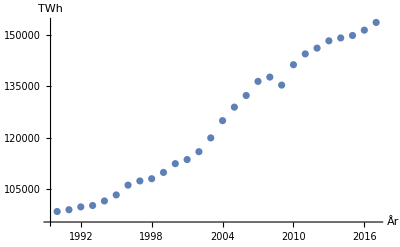

```mathematica
showtotalt=ListPlot[totalt,AxesLabel->{"År","TWh"}]
```

```mathematica
lmtotalt=Fit[totalt,{1,x},x]
```

-4.51374×10^6+2314.87 x

Vi ser att en linjär anpassning passar ganska bra till den totala energikonsumtionen. Ovan tog jag också fram en linjär anpassning till variablen lmtotalt.
Jag har i uppgift 2 summerat TWh för förnybara energislag. Jag kommer nu att addera kärnkraft till detta och då har vi totalen för koldioxidfria energikällor. Detta jämför jag sedan med den totala energikonsumtionen.

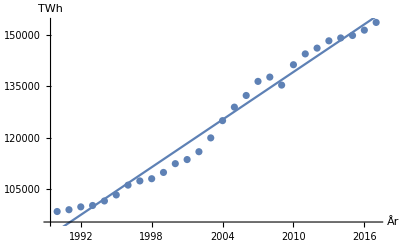

```mathematica
Show[showtotalt,Plot[lmtotalt,{x,1990,2017}]]
```

Här nedan använder jag listmanipulation för att addera TWh värdet från min lista renew från uppgift 2 där jag summerat ihop alla värden från förnybara energikällor. Jag tar ut tal nummer två från respektive talpar som ju består av:

```mathematica
{år,TWh}
```

Då får jag en lista med enbart TWh värdet. Detsamma gör jag från listan med kärnkraftsvärden. Sedan adderar jag dessa två listor, addrenew och addkarn. Sedan använder jag riffle för att sätta årtalet igen mellan varje TWh värdet. Därefter använder jag partition för att få tillbaka listan till originalform som nämnt ovan med år samt twh del. Detta hamnar i newlist2.

```mathematica
addrenew=renew[[2;;Length[renew],2]];
```

```mathematica
addkarn=karnkraft[[2;;Length[karnkraft],2]];
```

```mathematica
co2free=addkarn+addrenew;
```

```mathematica
y=Table[i,{i,1990,2017}]
```

{1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017}

```mathematica
newList=Riffle[y,co2free];
```

```mathematica
newList2=Partition[newList,2]
```

{{1990,15678.2},{1991,15835.3},{1992,16181.},{1993,16380.4},{1994,16751.2},{1995,17014.8},{1996,17047.3},{1997,17416.4},{1998,17746.3},{1999,17953.8},{2000,17971.4},{2001,18059.9},{2002,17882.2},{2003,18047.6},{2004,18126.},{2005,18237.5},{2006,18209.8},{2007,18377.9},{2008,18335.5},{2009,18623.5},{2010,18607.8},{2011,18640.},{2012,18868.5},{2013,19063.5},{2014,19208.2},{2015,19496.8},{2016,19742.3}}

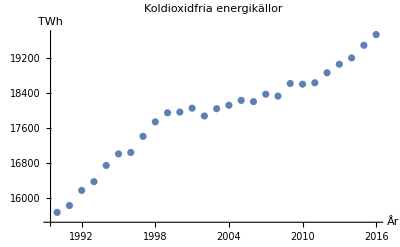

```mathematica
co2plot=ListPlot[newList2,AxesLabel->{"År","TWh"},PlotLabel->"Koldioxidfria energikällor"]
```

```mathematica
lmco2free=Fit[newList2,{1,x,x^2,x^3},x]
```

-4.44757×10^9+6.65543×10^6 x-3319.79 x^2+0.551985 x^3

Vi ser att en tredjegradsfunkton passar bra in på mätpunkterna.

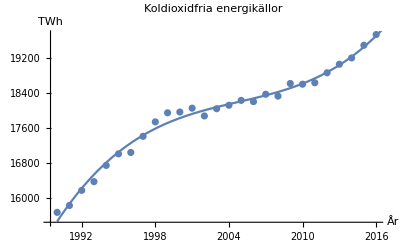

```mathematica
Show[co2plot,Plot[lmco2free,{x,1990,2017}]]
```

```mathematica
svar=Solve[lmtotalt==lmco2free,Reals]
```

{{x→2085.49}}

Ovanför har jag använt Solve för att lösa ekvationen och på så sätt se om det finns någon punkt där linjerna korsar varandra. Det visar sig att det finns det, nämligen år 2085.49.

```mathematica
twh==-4.513736680004535*^6+2314.8702127743127 2085.49
```

twh==313902.

twh är värdet på “y-axeln” vid det rätta årtalet då  linjerna korsar varandra. Jag har använt den anpassade linjens ekvation för totala energikonsumtionen och tryckt in x-värdet för att få fram detta svar som lagras i twh.

```mathematica
p1=Plot[lmtotalt,{x,1990,2100},AxesLabel->{"År","TWh"},Epilog->{PointSize[0.02],Red,Point[{2085.49,313902}]},PlotLabels->"Total konsumtion"]
```

-Graphics-

```mathematica
p2=Plot[lmco2free,{x,1990,2100},PlotLabels->"Koldioxidfri"];
```

```mathematica
Show[p1,p2,PlotRange->All]
```

-Graphics-

Enligt min modell skulle koldioxidfria energikällor gå om världens energikonsumtion år 2085, eller 2085.49 för att vara mer exakt. Detta skulle då markera punkten för när man skulle kunna stänga av allt som släpper ut koldioxid.

## Uppgift 4

### Vilket förnybart energislag uppskattas vara viktigast år 2050?

Vi tar fram en kurvanpassning till alla förnybara källor.

```mathematica
lmbio=Fit[biobransle,{1,x,x^2},x]
```

-2.94392×10^7+29417.8 x-7.34603 x^2

```mathematica
lmandraf=Fit[andrafornybara,{1,x,x^2},x]
```

2.85539×10^6-2867.33 x+0.719861 x^2

```mathematica
lmvatten=LinearModelFit[vatten,x,x]
```

FittedModel[-139968.+71.3453 x]

```mathematica
lmvind=Fit[vind,{1,x,x^2},x]
```

1.06775×10^7-10693.2 x+2.67722 x^2

```mathematica
lmsol=Fit[sol,{1,x,x^2,x^3},x]
```

-7.43012×10^8+1.11485×10^6 x-557.586 x^2+0.0929575 x^3

För solenergi blev det bäst passform med en tredjegradsfunktion. Eventuellt skulle en logaritmisk funktion bli lite bättre men det blev för små tal så fick errormeddelande.

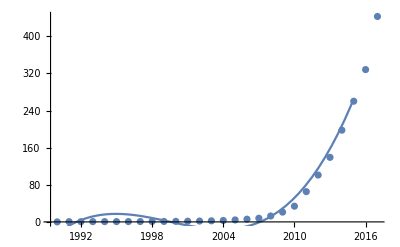

```mathematica
Show[ListPlot[sol],Plot[lmsol,{x,1990,2017}]]
```

För vindkraft blev en andragradsfunktion mest passande.

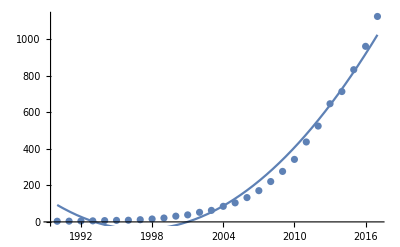

```mathematica
Show[ListPlot[vind],Plot[lmvind,{x,1990,2017}]]
```

För vattenkraft blev en linjär anpassning bäst.

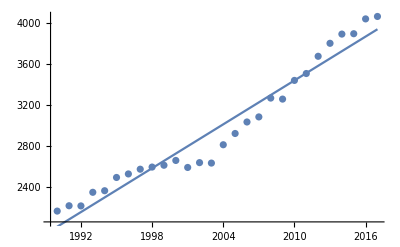

```mathematica
Show[ListPlot[vatten],Plot[lmvatten[x],{x,1990,2017}]]
```

För andra förnybara källor blev en andragradsfunktion bäst.

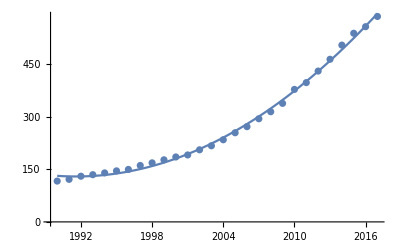

```mathematica
Show[ListPlot[andrafornybara],Plot[lmandraf,{x,1990,2017}]]
```

Nedan sparar jag graferna för de olika källorna i respektive variabler.

```mathematica
lmsoll=Plot[lmsol,{x,1990,2050},{PlotLabels->"Sol"}];
```

```mathematica
lmvindd=Plot[lmvind,{x,1990,2050},{PlotLabels->"Vind"},PlotStyle->Green];
```

```mathematica
lmandraff=Plot[lmandraf,{x,1990,2050},{PlotLabels->"Andra förnybara"},PlotStyle->Red];
```

```mathematica
lmbioo=Plot[lmbio,{x,1990,2050},PlotLabels->"Biobränsle",PlotStyle->Black];
```

För biobränsle blev en andragradsfunktion mest lik.

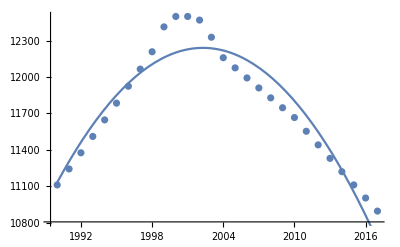

```mathematica
Show[ListPlot[biobransle],Plot[lmbio,{x,1990,2017}]]
```

Här nedan kan man se grafen för vatten.

```mathematica
hej =Plot[{lmvatten[x]},{x,1990,2050},AxesLabel->{"År","TWh"},PlotLabels->{"Vatten"},PlotLabel->"Förväntad konsumtion av förnybar energi",PlotStyle->Orange]
```

-Graphics-

```mathematica
Show[hej,lmbioo,lmandraff,lmvindd,lmsoll,PlotRange->All]
```

-Graphics-

Här ovan skriver vi ut de olika energikällorna och hur det är estimerat att användningen ser ut år 2050. Vi kan se att Sol står för den största ökningen. Således skulle, om min modell stämmer, solenergi vara absolut viktigast år 2050.

## Uppgift 5

### Vad har val av modell för betydelse?

Det har väldigt stor betydelse. Speciellt när man ser många år fram i tiden. Det kanske inte är så stor skillnad på olika kurvor inom ett litet årspann men det kan bli rejäla skillnader längre bort. Jämför t.ex. en rät linje med en tredjegradsfunktion.

## Uppgift 6

### Är ovanstående förutsägelser rimliga? Vilka felkällor finns?

Enligt mig är ovanstående förutsägelser orimliga. Det finns väldigt många felkällor. Dels så sträcker sig uppmätt data enbart över 27 år. Dels så påverkar forskning och utveckling samt det politiska klimatet hur energidistribution kan se ut. Det är orimligt att anta att utvecklingen för ett visst energislag ska följa samma väg som den gjort de senaste 27 åren. 
T.ex. så kan icke-förnybara energikällor inte fortsätta sin ökning för evigt. Samtidigt utvecklas andra tekniker snabbare idag än säg på 1990-talet,  vilket kanske ännu inte syns i uppmätt data.